# Get Map From Google Maps

## Héctor Manuel Sánchez Castellanos

## Functions

```mathematica
MarkContactsOnMap[map_,contactMatrix_,dataScenario_,worldSize_,scale_]:=Module[{cMatrix=contactMatrix,data=dataScenario,xNew,yNew,coordsNew,housesIndividuals,individualsCoords,rands,individualsCoordsFlattened,graph,map1=map,edgeshape,graph2},
xNew=((data[[1]]//Transpose)[[1]]+worldSize[[1]]/2);
yNew=((data[[1]]//Transpose)[[2]]+worldSize[[2]]/2);
coordsNew=scale*({xNew,yNew}//Transpose);
housesIndividuals={coordsNew,data[[2]]}//Transpose;
individualsCoords=Table[
rands=RandomReal[{-20,+20},{housesIndividuals[[i,2]],2}];
(#+housesIndividuals[[i,1]])&/@rands
,{i,1,housesIndividuals//Length}];
individualsCoordsFlattened=Flatten[individualsCoords,1];
graph=GraphTransitionsFrequenciesPlacing[cMatrix,individualsCoordsFlattened,ImageSize->worldSize];
graph2=HighlightGraph[graph,Map[Subgraph[graph,#]&, FindGraphCommunities[graph]]];
Show[{map1,graph2}]
]
```

```mathematica
edgeshape[e_,___]:={Arrowheads[{{.015,.9}}],Arrow[e]}
Options[GraphTransitionsFrequenciesPlacing]:={LineThickness->.0025,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->{"Scaled",.025},EdgeShapeFunction->edgeshape,VertexLabelStyle->Directive[Black,Italic,8]}
GraphTransitionsFrequenciesPlacing[frequenciesOutput_,placings_,OptionsPattern[]]:=Module[{frequencies,syllables,max,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
max=frequencies//Flatten//Max;
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,EdgeStyle->edgesStyleList,VertexCoordinates->placings,ImageSize->OptionValue[ImageSize],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle],VertexStyle->{LightBlue},VertexLabels->Placed["Name",Center],EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}]]
]
```

```mathematica
MarkHousesInMap[map_,dataScenario_,worldSize_,scale_]:=Module[{xNew,yNew,coordsNew,points,map1=map,data=dataScenario},
xNew=((data[[1]]//Transpose)[[1]]+worldSize[[1]]/2);
yNew=((data[[1]]//Transpose)[[2]]+worldSize[[2]]/2);
coordsNew=scale*({xNew,yNew}//Transpose);
points=Point[#]&/@coordsNew;
Show[{map1,Graphics[{PointSize[Large],points}]}]
]
```

```mathematica
MarkIndividualInMap[map_,dataScenario_,worldSize_,scale_]:=Module[{map1=map,coordsNew,xNew,yNew,points,housesIndividuals,data=dataScenario,individualsCoords,rands,individualsCoordsFlattened,individualsPoints},
xNew=((data[[1]]//Transpose)[[1]]+worldSize[[1]]/2);
yNew=((data[[1]]//Transpose)[[2]]+worldSize[[2]]/2);
coordsNew=scale*({xNew,yNew}//Transpose);
housesIndividuals={coordsNew,data[[2]]}//Transpose;
individualsCoords=Table[
rands=RandomReal[{-5,+5},{housesIndividuals[[i,2]],2}];
(#+housesIndividuals[[i,1]])&/@rands
,{i,1,housesIndividuals//Length}];
individualsCoordsFlattened=Flatten[individualsCoords,1];
individualsPoints=Point[#]&/@individualsCoordsFlattened;
points=Point[#]&/@coordsNew;
Show[{map1,Graphics[{Blue,PointSize[.03],points}],Graphics[{Red,individualsPoints}]}]
]
```

```mathematica
VertexNumberToVertexSyllable[syllables_,fixedEdgesList_]:=Table[DirectedEdge[syllables[[fixedEdgesList[[index]][[1]][[1]]]],syllables[[fixedEdgesList[[index]][[1]][[2]]]]->fixedEdgesList[[index]][[2]]]//N,{index,1,Length[fixedEdgesList]}]
Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
```

```mathematica
(<<SoNA3BSAnalysis`)//Quiet
(<<BehaviorSpaceInterface`)//Quiet
(<<PajaroLoco`)//Quiet
SetDirectory[NotebookDirectory[]];
TakeList[string_]:=StringSplit[StringTake[string,{StringPosition[string,"(list"][[1,2]]+1,(string//Length)-2}]]//ToExpression
GetDataSets[scenario_]:=Module[{scenarioList,positions,setsRaw,listsStart,listsEnd,elementsLists},
scenarioList=StringTrim[StringSplit[scenario,"\n"]];
positions=Drop[Position[StringPosition[scenarioList,#],a_/;Length[a]>1],-1][[1,1]]&/@{"set xcord","set ycord","set individuals","set names_listg"};
setsRaw=scenarioList[[positions]];
listsStart=StringPosition[#,"(list "][[1,2]]&/@setsRaw;
listsEnd=StringPosition[#,")"][[1,2]]&/@setsRaw;
elementsLists=ToExpression[StringTake[#[[1]],{#[[2]],#[[3]]}]//StringSplit]&/@({setsRaw,listsStart,listsEnd-1}//Transpose);
{
{elementsLists[[1]],elementsLists[[2]]}//Transpose,
elementsLists[[3]],
elementsLists[[4]]
}
]
```

```mathematica
GetMap[center_,zoom_,size_]:=Module[{root,cen,zoo,si,tail},
root="http://maps.googleapis.com/maps/api/staticmap?";
cen="center="<>ToString[center[[1]]]<>","<>ToString[center[[2]]]<>"&";
zoo="zoom="<>ToString[zoom]<>"&";
si="size="<>ToString[size[[1]]]<>"x"<>ToString[size[[2]]]<>"&";
tail="maptype=satellite&scale=2";
Import[root<>cen<>zoo<>si<>tail]
]
GetMapRoad[center_,zoom_,size_]:=Module[{root,cen,zoo,si,tail,road},
root="http://maps.googleapis.com/maps/api/staticmap?";
cen="center="<>ToString[center[[1]]]<>","<>ToString[center[[2]]]<>"&";
zoo="zoom="<>ToString[zoom]<>"&";
si="size="<>ToString[size[[1]]]<>"x"<>ToString[size[[2]]]<>"&";
tail="scale=2&";
road="style=feature:road.local%7Celement:geometry%7Ccolor:0x00ff00%7Cweight:1%7Cvisibility:on&style=feature:landscape%7Celement:geometry.fill%7Ccolor:0x000000%7Cvisibility:on&7Cinvert_lightness:true&style=feature:poi%7Cvisibility:off&style=feature:administrative%7Celement:labels%7Cweight:0%7Cvisibility:off%";
Print[root<>cen<>zoo<>si<>tail<>road];
Import[root<>cen<>zoo<>si<>tail<>road]
]
ConvertMapToBinaryCVS[data_]:=Module[{binarizedMap,tempString,newData,iS,jS,dS,path,lastPart,fullPath},
tempString="";
newData=Table[
Table[
iS=ToString[i];
jS=ToString[j];
dS=ToString[data[[i]][[j]]];
tempString=StringJoin[tempString,StringJoin[jS,"\t",iS,"\t",dS, "\n"]];
,{j,1,Length[data[[1]]]}]
,{i,1,Length[Transpose[data][[1]]]}];
tempString
]

MathematicaToNLogoList[list_]:=StringReplace[ToString[list],{"{"->"(list ","}"->")",","->""}]
ConvertToNetLogoCoordinates[coordinates_,imageDimensions_,scalingFactor_]:=Module[{dims=imageDimensions/2,newCoords},
newCoords=Floor/@({#[[1]]-dims[[1]],#[[2]]-dims[[2]]}&/@coordinates);
Floor/@(newCoords/scalingFactor)
]
FindRoads[map2_,worldSize_]:=Module[{river,road,dataB,dataCSV,fixed},
river=Image[SelectComponents[MorphologicalComponents[ColorNegate[map2],0.82],"Length",-1]];
road=ImageApply[# {.5,1,.5}&,map2,Masking->Dilation[river,5]]//ColorSeparate;
dataB=road[[2]]//ImageResize[#,worldSize]&//Dilation[#,1]&//Blur[#,5]&//ImageReflect//Binarize;
dataCSV=ConvertMapToBinaryCVS[dataB//ImageData];
fixed=(*(worldSize[[1]]//ToString)<>"\t"<>(worldSize[[2]]//ToString)<>"\n"<>*)dataCSV;
{dataB,fixed}
]
chars=StringJoin@@#&/@Tuples[{CharacterRange["A","Z"],CharacterRange["A","Z"]}];
chars2=StringJoin@@#&/@Tuples[{CharacterRange["a","z"],CharacterRange["a","z"]}];
SetDirectory[NotebookDirectory[]]
MathematicaToNLogoList[list_]:=StringReplace[ToString[list],{"{"->"(list ","}"->")",","->""}]
GetMap[center_,zoom_,size_]:=Module[{root,cen,zoo,si,tail},
root="http://maps.googleapis.com/maps/api/staticmap?";
cen="center="<>ToString[center[[1]]]<>","<>ToString[center[[2]]]<>"&";
zoo="zoom="<>ToString[zoom]<>"&";
si="size="<>ToString[size[[1]]]<>"x"<>ToString[size[[2]]]<>"&";
tail="maptype=satellite&scale=2";
Import[root<>cen<>zoo<>si<>tail]
]
GetMapRoad[center_,zoom_,size_]:=Module[{root,cen,zoo,si,tail,road},
root="http://maps.googleapis.com/maps/api/staticmap?";
cen="center="<>ToString[center[[1]]]<>","<>ToString[center[[2]]]<>"&";
zoo="zoom="<>ToString[zoom]<>"&";
si="size="<>ToString[size[[1]]]<>"x"<>ToString[size[[2]]]<>"&";
tail="scale=2&";
road="style=feature:road.local%7Celement:geometry%7Ccolor:0x00ff00%7Cweight:1%7Cvisibility:on&style=feature:landscape%7Celement:geometry.fill%7Ccolor:0x000000%7Cvisibility:on&7Cinvert_lightness:true&style=feature:poi%7Cvisibility:off&style=feature:administrative%7Celement:labels%7Cweight:0%7Cvisibility:off%";
Print[root<>cen<>zoo<>si<>tail<>road];
Import[root<>cen<>zoo<>si<>tail<>road]
]
ConvertMapToBinaryCVS[data_]:=Module[{binarizedMap,tempString,newData,iS,jS,dS,path,lastPart,fullPath},
tempString="";
newData=Table[
Table[
iS=ToString[i];
jS=ToString[j];
dS=ToString[data[[i]][[j]]];
tempString=StringJoin[tempString,StringJoin[jS,"\t",iS,"\t",dS, "\n"]];
,{j,1,Length[data[[1]]]}]
,{i,1,Length[Transpose[data][[1]]]}];
tempString
]

GenerateRandomScenario[housesNumber_,minMaxCoords_,minMaxAreas_,individualsScaling_,workZonesNumber_,scenarioNumber_]:=Module[{xCoords,yCoords,areas,individuals,individualsNames,housesNames,wzXCoords,wzYCoords,workNames,xCoordsS,yCoordsS,areasS,individualsS,individualsNamesS,housesNamesS,workNamesS,groups},
xCoords=RandomInteger[{-minMaxCoords[[1]],minMaxCoords[[1]]},housesNumber];
yCoords=RandomInteger[{-minMaxCoords[[2]],minMaxCoords[[2]]},housesNumber];
areas=RandomInteger[minMaxAreas,housesNumber];
individuals=areas/individualsScaling//Floor;
individualsNames=ToString["\""<>ToString[#]<>"\""&/@chars2[[1;;(individuals//Total)]]];
housesNames=ToString["\""<>ToString[#]<>"\""&/@chars[[1;;housesNumber]]];
wzXCoords=RandomInteger[{-minMaxCoords[[1]],minMaxCoords[[1]]},workZonesNumber];
wzYCoords=RandomInteger[{-minMaxCoords[[2]],minMaxCoords[[2]]},workZonesNumber];
workNames=Range[workZonesNumber];

xCoordsS=MathematicaToNLogoList[xCoords];
yCoordsS=MathematicaToNLogoList[yCoords];
areasS=MathematicaToNLogoList[areas];
individualsS=MathematicaToNLogoList[individuals];
individualsNamesS=MathematicaToNLogoList[individualsNames];
housesNamesS=MathematicaToNLogoList[housesNames];
workNamesS=MathematicaToNLogoList[workNames];
wzXCoords=MathematicaToNLogoList[wzXCoords];
wzYCoords=MathematicaToNLogoList[wzYCoords];
groups=MathematicaToNLogoList[Range[housesNumber]];

"to set-coordinates"<>ToString[scenarioNumber]<>"\n"<>
"\tset xcord "<>xCoordsS<>"\n"<>
"\tset ycord "<>yCoordsS<>"\n"<>
"\tset areas "<>areasS<>"\n"<>
"\tset groups "<>groups<>"\n"<>
"\tset individuals "<>individualsS<>"\n"<>
"\tset names_listg "<>individualsNamesS<>"\n"<>
"\tset names_houses "<>housesNamesS<>"\n"<>
"\tset names_workZones "<>workNamesS<>"\n"<>
"\tset wxcord "<>wzXCoords<>"\n"<>
"\tset wycord "<>wzYCoords<>"\n"<>
"\tset scenario_number "<>ToString[scenarioNumber]<>"\n"<>
"end\n"
]
```

/Users/chipdelmal/Google Drive/SoNAAABS/76_VisitingBehaviour/ParametersDefinition

```mathematica
GetWeather[{initialDate_,finalDate_},coords_]:=Module[{range,temps,data},
(*GetData*)
range=DateRange[initialDate,finalDate,{1,"Day"}];
temps=AirTemperatureData[
coords
,DateObject[#],
UnitSystem->"Metric"
]&/@range;
data=If[#[[1]]≠ 0,#[[1,1]]//Mean,0]&/@(temps/._Missing->{0})
]
WeatherString[{initialDate_,finalDate_},weatherData_]:=Module[{range},
range=DateRange[initialDate,finalDate,{1,"Day"}];
{#[[1,2]],#[[1,3]],#[[1,1]],#[[2]]}&/@({range,weatherData}//Transpose)//Prepend[#,{}]&
]
```

```mathematica
FindHouses[map_,morphoThreshold_,minSize_,maxSize_,rectangularity_]:=Module[{morpho,img1,m,img2,common,replaced,m2,multi,coords,final,map2=ImageTake[map, {50,ImageDimensions[map][[2]]},{0,ImageDimensions[map][[1]]}]},
morpho=MorphologicalComponents[map2,morphoThreshold,CornerNeighbors->True]//Colorize;
img1=ImageCompose[map2,{morpho,.5}];
m=SelectComponents[morpho,{"BoundingBoxArea","BoundingBoxArea","Rectangularity"},#1>minSize&&#2<maxSize&&#3>rectangularity&,-1]//Colorize;
img2=ImageCompose[map2,{m,.75}];
common=Commonest[Flatten[ImageData[m],1]][[1]];
replaced=Map[If[#==common,{0,0,0},#]&,m//ImageData,{2}];
m2=replaced//Image;
multi=ImageMultiply[map2,m2];
coords=ComponentMeasurements[multi//ImageReflect,{"Centroid","BoundingBoxArea"}];
final=Show[map2,Graphics[{Red,Thick,Circle[#[[1]],#[[2]]]&/@ComponentMeasurements[multi,{"Centroid","EquivalentDiskRadius"}][[All,2]]}]];
{{img1//ImageReflect,img2//ImageReflect,multi//ImageReflect,final//ImageReflect},coords}
]
CreateStringCoordinatesAndAreas[coordinates_,areas_,individualsScaling_,gravities_]:=Module[{temp,coords,xcoords,workPosition,ycoords,areasNL,coordsString,groupsNL,individualsNL,individualsNamesL,housesNamesL,workNamesL},
temp=ToString[#]&/@(coordinates//Transpose);
coords=StringReplace[#,{"{"->"(list ","}"->")",","->""}]&/@temp;
xcoords=coords[[1]];ycoords=coords[[2]];
coordsString="set xcord "<>xcoords <>"\n"<>"set ycord "<>ycoords<>"\n";
areasNL="set areas \n"<>StringReplace[ToString[areas],{"{"->"(list ","}"->")",","->""}];
groupsNL="set groups \n"<>StringReplace[ToString[Range[areas//Length]],{"{"->"(list ","}"->")",","->""}];
individualsNL="set individuals \n"<>StringReplace[ToString[areas/individualsScaling//Floor],{"{"->"(list ","}"->")",","->""}];
individualsNamesL="set names_listg \n"<>StringReplace[ToString["\""<>ToString[#]<>"\""&/@chars2[[1;;Total[areas/individualsScaling//Floor]]]],{"{"->"(list ","}"->")",","->""}];
(*individualsNamesL="set names_listg \n"<>StringReplace[ToString[Range[areas/individualsScaling//Floor//Total]],{"{"->"(list ","}"->")",","->""}];*)
(*housesNamesL="set names_houses \n"<>StringReplace[ToString[Range[coordinates//Length]],{"{"->"(list ","}"->")",","->""}];*)
housesNamesL="set names_houses \n"<>StringReplace[ToString["\""<>ToString[#]<>"\""&/@chars[[1;;(coordinates//Length)]]],{"{"->"(list ","}"->")",","->""}];
workNamesL="set names_workZones \n"<>StringReplace[ToString[Range[1]],{"{"->"(list ","}"->")",","->" "}];
workPosition="set wxcord \n(list 0)\n"<>"\tset wycord \n(list 0)\n"<>"set scenario_number \n\"GMap\"\n";
(**)
"to set-coordinates \n"<>"\t"<>coordsString<>"\t"<>areasNL<>"\n\t"<>groupsNL<>"\n\t"<>individualsNL<>"\n\t"<>individualsNamesL<>"\n\t"<>housesNamesL<>"\n\t"<>workNamesL<>"\n\t"<>workPosition<>"set gravities "<>gravities<>"\n\t"<>"end"
]
```

## Get Map

```mathematica
(*Parameters*)
datesRange={{2008,1,1},{2012,1,1}};
coords={18.4311529,-95.0903019};
worldSize={2700 ,1800};
{zoom,size,scale}={18,1000,2};
{scaling,individualsScaling}={1,25};
```

```mathematica
(*WeatherData*)
wd=GetWeather[datesRange,coords];
ws=WeatherString[datesRange,wd];
tempLP=ListPlot[wd,Joined->True];
(*Export["weather.csv",ws]*)
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1→{{104.865,145.327},88},2→{{211.524,137.968},252},3→{{110.944,132.29},108},4→{{94.7564,112.782},48},5→{{208.375,116.025},152},6→{{209.091,105.682},36},7→{{200.19,102.569},48},8→{{143.818,94.5118},104},9→{{202.21,94.8226},49},10→{{112.17,93.8956},96},11→{{79.7083,89.7083},196},12→{{168.914,85.2931},40},13→{{146.02,82.3},32},14→{{218.5,76.0333},35},15→{{188.816,71.0789},64},16→{{223.335,61.3678},288},17→{{234.844,47.2188},45},18→{{38.2368,35.7632},30},19→{{290.038,35.5769},21},20→{{9.63333,26.8333},24},21→{{280.438,22.2875},143}}}

{{{104.865,145.327},{211.524,137.968},{110.944,132.29},{94.7564,112.782},{208.375,116.025},{209.091,105.682},{200.19,102.569},{143.818,94.5118},{202.21,94.8226},{112.17,93.8956},{79.7083,89.7083},{168.914,85.2931},{146.02,82.3},{218.5,76.0333},{188.816,71.0789},{223.335,61.3678},{234.844,47.2188},{38.2368,35.7632},{290.038,35.5769},{9.63333,26.8333},{280.438,22.2875}},{88,252,108,48,152,36,48,104,49,96,196,40,32,35,64,288,45,30,21,24,143}}

to set-coordinates 
	set xcord (list -46 61 -40 -56 58 59 50 -7 52 -38 -71 18 -4 68 38 73 84 -112 140 -141 130)
set ycord (list 45 37 32 12 16 5 2 -6 -6 -7 -11 -15 -18 -24 -29 -39 -53 -65 -65 -74 -78)
	set areas 
(list 88 252 108 48 152 36 48 104 49 96 196 40 32 35 64 288 45 30 21 24 143)
	set groups 
(list 1 2 3 4 5 6 7 8 9 10 11 12 13 14 15 16 17 18 19 20 21)
	set individuals 
(list 3 10 4 1 6 1 1 4 1 3 7 1 1 1 2 11 1 1 0 0 5)
	set names_listg 
(list "aa" "ab" "ac" "ad" "ae" "af" "ag" "ah" "ai" "aj" "ak" "al" "am" "an" "ao" "ap" "aq" "ar" "as" "at" "au" "av" "aw" "ax" "ay" "az" "ba" "bb" "bc" "bd" "be" "bf" "bg" "bh" "bi" "bj" "bk" "bl" "bm" "bn" "bo" "bp" "bq" "br" "bs" "bt" "bu" "bv" "bw" "bx" "by" "bz" "ca" "cb" "cc" "cd" "ce" "cf" "cg" "ch" "ci" "cj" "ck" "cl")
	set names_houses 
(list "AA" "AB" "AC" "AD" "AE" "AF" "AG" "AH" "AI" "AJ" "AK" "AL" "AM" "AN" "AO" "AP" "AQ" "AR" "AS" "AT" "AU")
	set names_workZones 
(list 1)
	set wxcord 
(list 0)
	set wycord 
(list 0)
set scenario_number 
"GMap"
set gravities (list (list 0. 0.0288923 0.684021 0.0541637 0.0172122 0.00379403 0.00576306 0.0332461 0.00533933 0.0466204 0.0689305 0.00680221 0.00740116 0.00258925 0.00667743 0.0179007 0.00222372 0.00239088 0.000593953 0.00136097 0.00407708) (list 0.0138054 0. 0.0190828 0.00603207 0.554635 0.0615773 0.0622996 0.0288119 0.045098 0.0145717 0.0178366 0.0156256 0.00776498 0.0161562 0.0229991 0.0859692 0.00919116 0.00132911 0.00226183 0.000810301 0.0141426) (list 0.544351 0.0317823 0. 0.0956034 0.0199388 0.00445591 0.00694349 0.0530782 0.00644358 0.0832674 0.0899513 0.00919294 0.0109826 0.00304061 0.00834953 0.0208712 0.00254986 0.00262929 0.000648797 0.00143643 0.00448288) (list 0.0977335 0.0227791 0.21677 0. 0.0151747 0.00353838 0.0055177 0.0489421 0.00532499 0.187626 0.333145 0.00824828 0.0116033 0.00270922 0.00779764 0.0193717 0.00242619 0.00423985 0.000614258 0.00211545 0.00432289) (list 0.00547654 0.369326 0.00797185 0.00267579 0. 0.241203 0.139361 0.016176 0.0723831 0.00709498 0.00818444 0.0115159 0.00458598 0.0148119 0.0191841 0.0645934 0.00596328 0.000610544 0.00115096 0.000364257 0.00736718) (list 0.00251047 0.0852724 0.00370493 0.00129754 0.501611 0. 0.191487 0.00841268 0.105171 0.00357249 0.00409112 0.00699024 0.00250884 0.012832 0.014115 0.0471538 0.00391145 0.000312271 0.000649634 0.000185079 0.00421151) (list 0.00345679 0.0782059 0.00523346 0.00183418 0.262719 0.173582 0. 0.0137511 0.327823 0.00526176 0.00572412 0.013434 0.0041015 0.0144376 0.0244789 0.0552932 0.0045243 0.000419095 0.000716831 0.000244728 0.0047585) (list 0.0314747 0.0570857 0.0631433 0.0256784 0.0481309 0.0120365 0.0217039 0. 0.0210708 0.140488 0.0695325 0.0820504 0.304718 0.00867025 0.0364576 0.0568993 0.00627052 0.00301309 0.00123889 0.00155805 0.00877976) (list 0.00388188 0.0686194 0.00588671 0.00214555 0.165396 0.115558 0.397351 0.0161814 0. 0.0062815 0.00691705 0.0176925 0.00512257 0.0300258 0.045688 0.0975988 0.00716682 0.00052397 0.000992605 0.000305276 0.00666593) (list 0.0541452 0.0354184 0.121521 0.120765 0.025898 0.0062705 0.0101882 0.172346 0.0100344 0. 0.303771 0.0201635 0.0415011 0.00499896 0.0166164 0.0356443 0.00433708 0.00563124 0.000995142 0.00265463 0.00709997) (list 0.074301 0.0402373 0.121837 0.199013 0.027727 0.00666456 0.0102866 0.0791681 0.0102553 0.281932 0. 0.0157763 0.0226138 0.00566155 0.0164354 0.0422791 0.00547226 0.0203861 0.00140073 0.00851889 0.0100342) (list 0.0156024 0.0750091 0.0264964 0.010485 0.0830181 0.0242315 0.0513722 0.198793 0.0558182 0.0398221 0.033571 0. 0.0820176 0.0187937 0.146196 0.111345 0.0106073 0.00209884 0.00167374 0.00113908 0.0119084) (list 0.0137586 0.0302098 0.0256549 0.0119541 0.026794 0.00704843 0.0127115 0.598343 0.013098 0.0664275 0.0389999 0.066472 0. 0.0058583 0.0289652 0.0397669 0.00437095 0.00192822 0.000811515 0.000980774 0.00584602) (list 0.00286342 0.0373924 0.00422533 0.00166042 0.0514815 0.0214463 0.0266185 0.0101279 0.0456718 0.00475998 0.00580848 0.00906109 0.00348504 0. 0.040731 0.696174 0.0236362 0.000506857 0.00179208 0.000300434 0.0122569) (list 0.00975101 0.0702888 0.0153212 0.00631056 0.0880469 0.0311508 0.0595954 0.0562352 0.0917672 0.0208927 0.0222658 0.0930754 0.0227533 0.0537844 0. 0.311723 0.023301 0.00174546 0.0025401 0.000980589 0.0184708) (list 0.00713124 0.0716756 0.010448 0.00427687 0.0808749 0.0283895 0.0367236 0.0239431 0.053479 0.0122264 0.0156256 0.0193386 0.00852202 0.250786 0.08504 0. 0.231132 0.001468 0.00701535 0.000875062 0.0510294) (list 0.00296999 0.025691 0.00427939 0.00179583 0.0250318 0.00789516 0.0100741 0.00884625 0.0131658 0.00498757 0.00678047 0.00617647 0.00314035 0.0285459 0.0213113 0.774892 0. 0.000692296 0.00590691 0.000420078 0.0473974) (list 0.0382148 0.0444597 0.0528082 0.0375568 0.0306705 0.00754312 0.0111677 0.0508703 0.0115192 0.0774982 0.30229 0.0146255 0.0165789 0.00732569 0.0191048 0.0588983 0.00828491 0. 0.00236509 0.190865 0.0173535) (list 0.00282447 0.0225102 0.00387689 0.00161882 0.0172019 0.00466874 0.00568304 0.00622293 0.00649241 0.0040746 0.00617952 0.00347001 0.00207591 0.00770605 0.0082717 0.0837412 0.0210314 0.000703654 0. 0.000453495 0.791193) (list 0.0364547 0.0454241 0.0483483 0.0314031 0.0306651 0.0074922 0.0109287 0.0440825 0.0112472 0.0612244 0.211693 0.0133021 0.0141319 0.00727688 0.0179867 0.058837 0.00842481 0.31986 0.00255443 0. 0.0186626) (list 0.00855036 0.0620723 0.0118136 0.00502428 0.0485587 0.0133481 0.0166374 0.019449 0.0192283 0.0128206 0.0195224 0.010888 0.00659511 0.0232438 0.0265264 0.268634 0.0744241 0.00227693 0.348926 0.00146117 0.))
	end

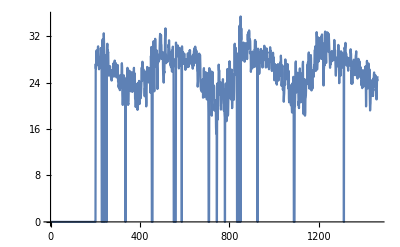
{-Graphics-,-Graphics-}

```mathematica
(*MapAndHouses*)
map=GetMap[coords,zoom,worldSize];
houses=FindHouses[ImageResize[map//ImageReflect,{300,200}],.45,20,1000,.25]
(*HousesExport*)
{coordinates,areas}={(houses//Last)[[All,2,1]],(houses//Last)[[All,2,2]]}
(**)
k=1;
distancesMatrix=Table[EuclideanDistance[i,#]&/@coordinates,{i,coordinates}];
massesMatrix=Table[i*areas,{i,areas}];
gravity=Quiet[massMatrix/distancesMatrix];
gravityProbability=(#/Total[#])&/@ReplaceAll[gravity,Indeterminate->0];netLogoGravityLists=MathematicaToNLogoList[#]&/@gravityProbability;
gravitiesList=MathematicaToNLogoList[netLogoGravityLists];
(**)
dims=ImageDimensions[ImageResize[map//ImageReflect,{300,200}]];
coordinatesNLogo=ConvertToNetLogoCoordinates[coordinates,dims,scaling];
CreateStringCoordinatesAndAreas[coordinatesNLogo,areas,individualsScaling,gravitiesList]
(*Export[ParentDirectory[]<>"/GoogleMap.nls",%,"Text"];*)
{tempLP,houses[[1,4]]}
(*Export["map.png",houses[[1,4]]]*)
```